# Calcolo della Risposta Forzata per un sistema LTI-TD

```mathematica
A={{0,1,0},{0,0,1},{-1/30,1/5,1/30}}
```

{{0,1,0},{0,0,1},{-1/30,1/5,1/30}}

```mathematica
A//MatrixForm
```

(0 | 1 | 0
0 | 0 | 1
-1/30 | 1/5 | 1/30)

```mathematica
B={{0},{0},{1}}
```

{{0},{0},{1}}

```mathematica
Cc={1,3,0}
```

{1,3,0}

Inizio con il calcolo della FdT del sistema che, nel caso D=0 vale

```mathematica
G[z_]:=Simplify[Cc.Inverse[z IdentityMatrix[3]-A].B][[1]]
```

```mathematica
G[z]
```

(30+90 z)/(1-6 z-z^2+30 z^3)

Calcolo zeri e poli

```mathematica
Solve[Numerator[G[z]]==0,z]
```

{{z→-1/3}}

```mathematica
Solve[Denominator[G[z]]==0,z]
```

{{z→-1/2},{z→1/5},{z→1/3}}

Calcolo la risposta al gradino



che, nel nostro caso e’ espandibile nella forma compatibile con il fratto semplice 



il calcolo dei coefficienti si puo’ ottenere con la seguente formula di Heaviside adattata per la trasformata zeta

```mathematica
Subscript[C, 0]=lim_(z->0) (G[z] z)/(z-1)
```

0

```mathematica
Subscript[C, 1]=lim_(z->-1/2) (z+1/2)/z((G[z] z)/(z-1))
```

4/7

```mathematica
Subscript[C, 2]=lim_(z->1/3) (z-1/3)/z((G[z] z)/(z-1))
```

-27

```mathematica
Subscript[C, 3]=lim_(z->1/5) (z-1/5)/z((G[z] z)/(z-1))
```

150/7

```mathematica
Subscript[C, 4]=lim_(z->1) (z-1)/z((G[z] z)/(z-1))
```

5

Mi scrivo la Z-trasformata decomposta nella somma dei quattro fratti semplici

```mathematica
Subscript[C, 0]+Subscript[C, 1] z/(z+1/2)+Subscript[C, 2] z/(z-1/3)+Subscript[C, 3] z/(z-1/5)+Subscript[C, 4] z/(z-1)
```

(5 z)/(-1+z)-(27 z)/(-1/3+z)+(150 z)/(7 (-1/5+z))+(4 z)/(7 (1/2+z))

Definiamo la risposta al gradino in z

```mathematica
Subscript[Y, f][z_]:=G[z]/(z-1)z
```

```mathematica
Subscript[y, -1][k_]:=InverseZTransform[G[z]/(z-1)z,z,k]
```

```mathematica
Subscript[y, -1][k]
```

5+1/7 (-1)^k 2^(2-k)-3^(3-k)+(6 5^(2-k))/7

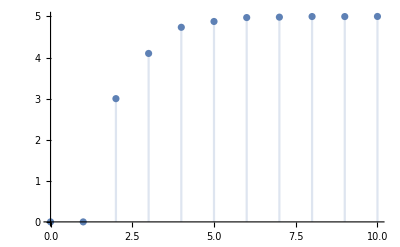

```mathematica
DiscretePlot[Subscript[y, -1][k],{k,0,10},PlotRange->All]
```

```mathematica
Subscript[Y, f][z]
```

(z (30+90 z))/((-1+z) (1-6 z-z^2+30 z^3))

```mathematica
Apart[(Subscript[Y, f][z])/z]
```

5/(-1+z)+8/(7 (1+2 z))-81/(-1+3 z)+750/(7 (-1+5 z))

```mathematica
Expand[z Apart[(Subscript[Y, f][z])/z]]
```

(5 z)/(-1+z)+(8 z)/(7 (1+2 z))-(81 z)/(-1+3 z)+(750 z)/(7 (-1+5 z))

Voglio calcolare la risposta all’impulso del sistema


metodo 1, scrivo la FdT come somma di tre fratti semplici compatibili

```mathematica
Subscript[D, 0]+Subscript[D, 1]  z/(z+1/2)+Subscript[D, 2]  z/(z-1/3)+Subscript[D, 3]  z/(z-1/5)
```

30+(54 z)/(-1/3+z)-(600 z)/(7 (-1/5+z))+(12 z)/(7 (1/2+z))

mi calcolo i fratti semplici adattando la Formula di Heaviside alla Z-trasformata

```mathematica
Subscript[D, 0]=lim_(z->0) G[z]
```

30

```mathematica
Subscript[D, 1]=lim_(z->-1/2) (z+1/2)/z G[z]
```

12/7

```mathematica
Subscript[D, 2]=lim_(z->1/3) (z-1/3)/z G[z]
```

54

```mathematica
Subscript[D, 3]=lim_(z->1/5) (z-1/5)/z G[z]
```

-600/7

```mathematica
Subscript[D, 0]+Subscript[D, 1]  z/(z+1/2)+Subscript[D, 2]  z/(z-1/3)+Subscript[D, 3]  z/(z-1/5)
```

30+(54 z)/(-1/3+z)-(600 z)/(7 (-1/5+z))+(12 z)/(7 (1/2+z))

```mathematica
g[k_]:=InverseZTransform[G[z],z,k]
```

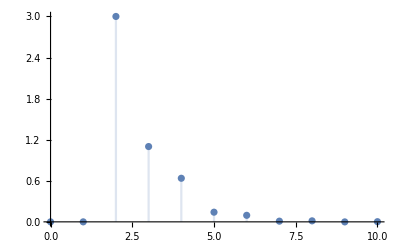

```mathematica
DiscretePlot[g[k],{k,0,10},PlotRange->All]
```

Metodo nr. 2

```mathematica
Subscript[E, 0] 1/z+Subscript[E, 1] 1/(z+1/2)+Subscript[E, 2] 1/(z-1/3)+Subscript[E, 3] 1/(z-1/5)
```

54/(-1/3+z)-600/(7 (-1/5+z))+30/z+12/(7 (1/2+z))

```mathematica
Subscript[E, 0]=lim_(z->0) z(G[z]/z)
```

30

```mathematica
Subscript[E, 1]=lim_(z->-1/2) (z+1/2)(G[z]/z)
```

12/7

```mathematica
Subscript[E, 2]=lim_(z->1/3) (z-1/3)(G[z]/z)
```

54

```mathematica
Subscript[E, 3]=lim_(z->1/5) (z-1/5)(G[z]/z)
```

-600/7

```mathematica
Fratti=Subscript[E, 0] 1/z+Subscript[E, 1] 1/(z+1/2)+Subscript[E, 2] 1/(z-1/3)+Subscript[E, 3] 1/(z-1/5)
```

54/(-1/3+z)-600/(7 (-1/5+z))+30/z+12/(7 (1/2+z))

```mathematica
Expand[z Fratti]
```

30+(54 z)/(-1/3+z)-(600 z)/(7 (-1/5+z))+(12 z)/(7 (1/2+z))